## Variables and help functions

```mathematica
numberOfAgents = 100;
donationCost = -10;
buyCost = -40;
donationHealthChange=7;
usageUtil = 5;
waitCost = -1;
fullToolHealth=10;

agentParams = Array[Function[x,
{(*RandomReal[0.4], (* How often a tool is needed *)*)
0.5,
RandomReal[], (* Prob to buy tool *)
RandomReal[], (* Prob to donate *)
0, (* Has tool (tool health) *)
0 (* payoff *)
}],numberOfAgents];
```

Calculate payoff now has a max number of tools so that a player that donates doesn’t have to if the pool is full.

```mathematica
(* Returns the utility, the updated agent, and change in poolHealth.
int, agent, int *)
CalculatePayoff[agent_,nPTools_,maxPTools_]:=Module[
{p=agent[[1]],pb=agent[[2]],
pd=agent[[3]],toolHealth=agent[[4]],
util=agent[[5]],poolHealthChange=0},
If[RandomReal[]<p,
If[toolHealth>0,
util+=usageUtil; toolHealth-=1,
If[RandomReal[]<pb,
toolHealth=fullToolHealth;
util+=buyCost+usageUtil,
If[nPTools>0,
util+=usageUtil;poolHealthChange-=1,
util+=waitCost]
]
],
If[RandomReal[]<pd &&nPTools<=maxPTools,
poolHealthChange+=donationHealthChange;
util+=donationCost,
util+=0
]
];
{{p,pb,pd,toolHealth,util},poolHealthChange}
];

CalculatePayoff[{0,0,1,5,0},3,4]
```

{{0,0,1,5,-10},7}

```mathematica
MutateValue[v_] := Module[{value},
If[v>0.5,distance = 1-v,distance =v];
value=RandomVariate[NormalDistribution[v,(*distance/4)+*)0.1]];
If[value<=0,0,Min[value,1]]
];
MutateValue[0.1]
MutateAgent[agent_]:=Module[
{p=agent[[1]],pb=agent[[2]],pd=agent[[3]],a4=agent[[4]],a5=agent[[5]]},
{p,MutateValue[pb],MutateValue[pd],a4,a5}
];
```

0.131627

## doround

```mathematica
DoRound[agentList_,initPoolHealth_,iterations_]:=Module[
{poolHealth=initPoolHealth,
agents=agentList,
agentPayoffs=ConstantArray[0,Length[agentList]],
PHhistory = {},
maxPoolTools=Length[agentList]*1.2},
For[i=0,i<iterations,i++,
nPoolTools=poolHealth/fullToolHealth;
(*agents=RandomSample[agents];*)
agents=Sort[agents,#1[[3]]>#2[[3]]&];
For[j=1,j≤Length[agents],j++,
{newAgent, healthChange}=CalculatePayoff[agents[[j]],nPoolTools,maxPoolTools];
agents[[j]]=newAgent;
poolHealth+=healthChange;
nPoolTools=poolHealth/fullToolHealth;
];

PHhistory = Append[PHhistory,poolHealth];
];
{agents, PHhistory}
];
```

## Simulation with pool resetting

Simulation clears pool health after each round. This means that mutated agents start with a new pool.

```mathematica
RunSim[agentList_]:=Module[{agents=agentList,history={}},
For[k=1,k<50,k++,
{ag, ph} =DoRound[agents,80,100];
(*Print[Map[Function[a,Last[a]],ag]];*)
rankedAgents=Sort[ag,Last[#1]>Last[#2]&];
newAgents=Take[rankedAgents,Length[rankedAgents]/4];
newAgents=Join[newAgents,newAgents,newAgents,newAgents];
newAgents=Map[Function[a,{a[[1]],a[[2]],a[[3]],0,0}],newAgents];
(* Mutate agents *)
newAgents=Map[Function[a,If[RandomReal[]<0.1,MutateAgent[a],a]],newAgents];
agents=newAgents;
history=Append[history, ph];
];
{ag, ph} =DoRound[agents,80,100];
history=Append[history, ph];
{ag, history}
];
```

### results

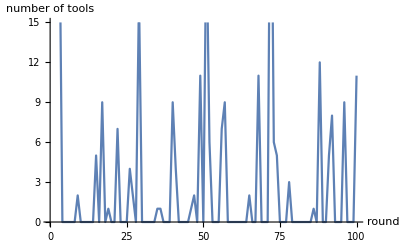

67.45

{{0.5,0,0.083511,0,164},{0.5,0,0.083511,0,151},{0.5,0,0.0789238,0,138},{0.5,0,0.0789238,0,137},{0.5,0,0.083511,0,127},{0.5,0,0.083511,0,126},{0.5,0,0.083511,0,124},{0.5,0,0.0663291,0,121},{0.5,0,0.0663291,0,120},{0.5,0,0.0420056,0,117},{0.5,0,0.0663291,0,116},{0.5,0,0.0789238,0,109},{0.5,0,0.0663291,0,108},{0.5,0,0.0789238,0,107},{0.5,0,0.083511,0,107},{0.5,0,0.0789238,0,103},{0.5,0,0.0789238,0,101},{0.5,0,0.0789238,0,100},{0.5,0,0.0663291,0,99},{0.5,0,0.0789238,0,97},{0.5,0,0.0789238,0,96},{0.5,0,0.0789238,0,96},{0.5,0,0.0420056,0,93},{0.5,0,0.0789238,0,90},{0.5,0,0.0663291,0,89},{0.5,0,0.083511,0,89},{0.5,0.0249465,0,0,87},{0.5,0,0.0663291,0,87},{0.5,0,0.0789238,0,87},{0.5,0,0.0623843,0,86},{0.5,0,0.083511,0,83},{0.5,0,0.0536429,0,80},{0.5,0,0.0789238,0,78},{0.5,0,0.0789238,0,78},{0.5,0,0.0789238,0,77},{0.5,0,0.0789238,0,77},{0.5,0,0.083511,0,77},{0.5,0,0.0789238,0,74},{0.5,0,0.083511,0,73},{0.5,0,0.0420056,0,72},{0.5,0,0.0789238,0,72},{0.5,0,0.083511,0,72},{0.5,0,0.0623843,0,69},{0.5,0,0.0663291,0,69},{0.5,0,0.0663291,0,69},{0.5,0,0.0663291,0,69},{0.5,0,0.0663291,0,68},{0.5,0,0.083511,0,68},{0.5,0,0.083511,0,68},{0.5,0,0.0789238,0,67},{0.5,0,0.0789238,0,67},{0.5,0,0.0536429,0,65},{0.5,0,0.0663291,0,65},{0.5,0,0.0789238,0,64},{0.5,0,0.0789238,0,64},{0.5,0,0.0789238,0,64},{0.5,0,0.0789238,0,64},{0.5,0,0.083511,0,64},{0.5,0,0.0623843,0,63},{0.5,0,0.0663291,0,63},{0.5,0,0.083511,0,63},{0.5,0,0,0,62},{0.5,0,0.0663291,0,60},{0.5,0,0.0789238,0,60},{0.5,0,0.083511,0,60},{0.5,0,0.0789238,0,59},{0.5,0,0.083511,0,58},{0.5,0,0.0789238,0,57},{0.5,0,0.083511,0,57},{0.5,0,0.083511,0,56},{0.5,0,0.0789238,0,55},{0.5,0,0.0420056,0,54},{0.5,0,0.083511,0,54},{0.5,0,0.0420056,0,53},{0.5,0.116629,0.0773136,2,48},{0.5,0,0.0789238,0,47},{0.5,0,0.0789238,0,47},{0.5,0,0.0573289,0,46},{0.5,0.0404609,0.0109345,9,44},{0.5,0,0.083511,0,44},{0.5,0,0.083511,0,43},{0.5,0,0,0,42},{0.5,0,0.083511,0,37},{0.5,0.0480008,0,3,36},{0.5,0,0.083511,0,35},{0.5,0,0.0663291,0,30},{0.5,0,0.0536429,0,28},{0.5,0,0.0623843,0,24},{0.5,0,0.083511,0,24},{0.5,0,0.0663291,0,23},{0.5,0.108144,0.165892,0,21},{0.5,0,0.0663291,0,18},{0.5,0,0.0663291,0,15},{0.5,0,0.0789238,0,13},{0.5,0.105106,0.0985177,0,9},{0.5,0,0.0536429,0,5},{0.5,0,0.0420056,0,-7},{0.5,0,0.0420056,0,-8},{0.5,0,0.225493,0,-29},{0.5,0,0.18602,0,-73}}

```mathematica
{a,h}=RunSim[agentParams];
ListLinePlot[h[[-1]],AxesLabel->{"round", "number of tools"}]
N[Total[Map[Function[x,Last[x]],a]]/Length[a]] (*average payoff*)
Sort[a,Last[#1]>Last[#2]&]
```

We see that we get a mixed stable equilibrium where everyone donates a bit. Below we plot the evolution of pool health over the generations.

```mathematica
hh={};
For[i=1,i≤Length[h],i++,
For[j=1,j≤Length[h[[i]]],j++,
hh=Append[hh,{i,j,h[[i]][[j]]}];
]
];
ListPlot3D[hh, AxesLabel->{evolutionNr,round,poolHealth}]
```

-Graphics3D-

## Simulation for not resetting tool usage

Simulation runs with agents mutating while pool is still functioning. Now if a lot of people donated in the past a new mutation can take advantage of this and vice versa.

```mathematica
RunSimContinuous[agentList_,initHealth_]:=Module[{agents=agentList,history={},avgPHist={},poolHealth=initHealth},
For[k=1,k<50,k++,
{ag, ph} =DoRound[agents,poolHealth,100];
(*Print[Map[Function[a,Last[a]],ag]];*)
rankedAgents=Sort[ag,Last[#1]>Last[#2]&];
newAgents=Take[rankedAgents,Length[rankedAgents]/2];
newAgents=Join[newAgents,newAgents];
newAgents=Map[Function[a,{a[[1]],a[[2]],a[[3]],0,0}],newAgents];
(* Mutate agents *)
newAgents=Map[Function[a,If[RandomReal[]<0.05,MutateAgent[a],a]],newAgents];
agents=newAgents;
avgP=N[Total[Map[Function[x,Last[x]],ag]]/Length[ag]];
avgPHist=Append[avgPHist,avgP];
history=Join[history, ph];
poolHealth=ph[[-1]];
];
{ag, ph} =DoRound[agents,poolHealth,100];
avgP=N[Total[Map[Function[x,Last[x]],ag]]/Length[ag]];
avgPHist=Append[avgPHist,avgP];
history=Join[history, ph];
{ag, history,avgPHist}
];
```

### Results

Run the model with 80 initial tools. We see a drop off after 500 rounds. This is probably because some agents realize that they can defect and be better of than anyone else. Or that they realize that they don’t have to buy tools and can just use the pool. Meaning that the pool runs out of tools. We also plot the average payoff for each round.

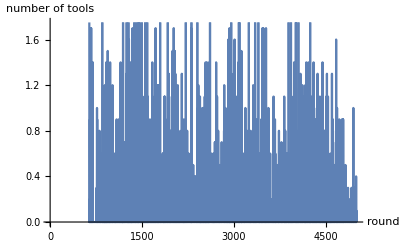

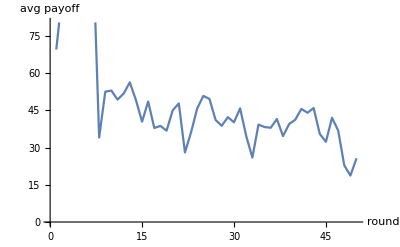

{{0.5,0.178368,0.00303923,0,84},{0.5,0.178368,0.00303923,3,80},{0.5,0.178368,0.00303923,0,78},{0.5,0.139714,0,0,72},{0.5,0.178368,0.00303923,0,67},{0.5,0.178368,0.00303923,0,66},{0.5,0.139714,0,0,64},{0.5,0.178368,0.00303923,0,63},{0.5,0.178368,0.00303923,0,63},{0.5,0.127003,0.0316845,0,60},{0.5,0.178368,0.00303923,0,58},{0.5,0.178368,0.00303923,6,56},{0.5,0.139714,0,0,52},{0.5,0.178368,0.00303923,7,52},{0.5,0.127003,0.0316845,0,50},{0.5,0.139714,0,0,49},{0.5,0,0.0522791,0,49},{0.5,0.139714,0,0,48},{0.5,0.139714,0,0,48},{0.5,0.139714,0,0,48},{0.5,0.245497,0,2,48},{0.5,0.139714,0,1,46},{0.5,0.178368,0.00303923,5,46},{0.5,0.139714,0,0,45},{0.5,0.139714,0,2,45},{0.5,0.139714,0,0,44},{0.5,0.139714,0,7,43},{0.5,0.139714,0,0,43},{0.5,0.139714,0,2,42},{0.5,0.245497,0,0,42},{0.5,0.139714,0,0,41},{0.5,0.178368,0.00303923,4,41},{0.5,0.178368,0.00303923,0,41},{0.5,0.139714,0,7,40},{0.5,0.139714,0,0,39},{0.5,0,0.0522791,0,39},{0.5,0.139714,0,5,34},{0.5,0.127003,0.0316845,10,33},{0.5,0,0.0522791,0,33},{0.5,0.178368,0.00303923,5,32},{0.5,0.178368,0.00303923,10,32},{0.5,0.139714,0,3,30},{0.5,0.139714,0,5,30},{0.5,0.178368,0.00303923,0,30},{0.5,0.139714,0,0,29},{0.5,0.139714,0,4,29},{0.5,0.178368,0.00303923,10,29},{0.5,0.139714,0,3,28},{0.5,0.178368,0.00303923,7,27},{0.5,0,0,0,25},{0.5,0.139714,0,0,25},{0.5,0.139714,0,2,25},{0.5,0.220605,0,8,24},{0.5,0,0.0522791,0,24},{0.5,0.245497,0,8,22},{0.5,0.178368,0.00303923,8,22},{0.5,0.127003,0.0316845,4,22},{0.5,0.19732,0,3,21},{0.5,0.139714,0,0,21},{0.5,0.127003,0.0316845,3,21},{0.5,0.127003,0.0316845,0,19},{0.5,0.245497,0,6,18},{0.5,0.139714,0,2,17},{0.5,0.178368,0.00303923,5,17},{0.5,0,0.0522791,0,17},{0.5,0,0.0522791,0,16},{0.5,0.139714,0,7,15},{0.5,0.127003,0.0316845,8,13},{0.5,0,0.0522791,0,13},{0.5,0.139714,0,0,12},{0.5,0.139714,0,4,12},{0.5,0.139714,0,8,12},{0.5,0,0.0522791,0,12},{0.5,0,0.0522791,0,11},{0.5,0.139714,0,0,8},{0.5,0,0.0522791,0,6},{0.5,0.139714,0,5,5},{0.5,0,0.0522791,0,5},{0.5,0,0.0522791,0,4},{0.5,0,0.0522791,0,4},{0.5,0.198418,0.0331838,6,3},{0.5,0,0.0522791,0,3},{0.5,0,0.0522791,0,1},{0.5,0,0.0522791,0,1},{0.5,0,0.0522791,0,1},{0.5,0.139714,0,4,0},{0.5,0,0.0522791,0,-2},{0.5,0,0.0522791,0,-4},{0.5,0,0.0522791,0,-5},{0.5,0.139714,0,10,-7},{0.5,0.127003,0.0316845,7,-9},{0.5,0,0.0522791,0,-9},{0.5,0,0.0522791,0,-10},{0.5,0,0,0,-18},{0.5,0,0.0522791,0,-18},{0.5,0,0.0522791,0,-20},{0.5,0,0.0522791,0,-24},{0.5,0,0.0522791,0,-26},{0.5,0,0.0522791,0,-30},{0.5,0,0.0522791,0,-36}}

```mathematica
{a,h,p}=RunSimContinuous[agentParams,800];
ListLinePlot[Map[Function[x, x/fullToolHealth],h],AxesLabel->{"round", "number of tools"}](* plot the number of tools in the pool at any given time *)
ListLinePlot[p,AxesLabel->{"round", "avg payoff"}]
Sort[a,Last[#1]>Last[#2]&]
```

We try the same thing but with fewer initial tools. This does not change much and a mixed strategy equilibrium can be observed here as well.

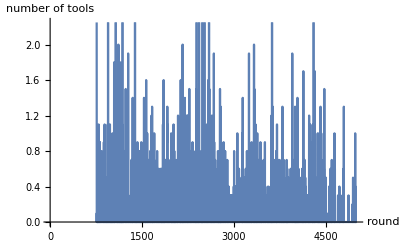

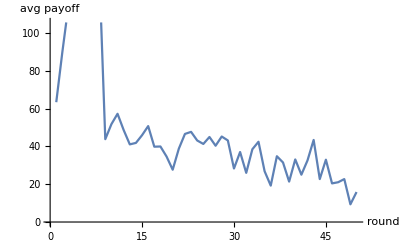

{{0.5,0,0.0024209,0,63},{0.5,0.145083,0.0152622,0,62},{0.5,0.329736,0,0,57},{0.5,0,0.0483259,0,54},{0.5,0.142616,0,2,52},{0.5,0,0.0483259,0,51},{0.5,0.329736,0,2,48},{0.5,0.142616,0,4,45},{0.5,0,0.0483259,0,44},{0.5,0.142616,0,1,43},{0.5,0.142616,0,0,42},{0.5,0.329736,0,3,42},{0.5,0.115578,0,0,42},{0.5,0.149673,0,3,40},{0.5,0,0.0024209,0,39},{0.5,0.149673,0,0,37},{0.5,0.142616,0,2,37},{0.5,0.142616,0,1,37},{0.5,0,0.0483259,0,37},{0.5,0.142616,0,5,36},{0.5,0.260584,0,7,36},{0.5,0,0.0483259,0,36},{0.5,0,0.0483259,0,36},{0.5,0.260584,0,4,35},{0.5,0.142616,0,0,34},{0.5,0.329736,0,8,34},{0.5,0.329736,0,5,32},{0.5,0.142616,0,4,31},{0.5,0.329736,0,9,31},{0.5,0.115578,0,0,30},{0.5,0.142616,0,5,30},{0.5,0,0.0483259,0,30},{0.5,0.142616,0,0,27},{0.5,0.260584,0,7,27},{0.5,0,0.0483259,0,27},{0.5,0,0.0483259,0,27},{0.5,0,0.0483259,0,27},{0.5,0.142616,0,10,26},{0.5,0.142616,0,6,25},{0.5,0,0.0024209,0,25},{0.5,0,0.0483259,0,25},{0.5,0.142616,0,0,24},{0.5,0,0.0483259,0,24},{0.5,0,0.0483259,0,24},{0.5,0.142616,0,6,23},{0.5,0.149673,0,6,22},{0.5,0.142616,0,10,22},{0.5,0.142616,0,4,21},{0.5,0.142616,0,0,20},{0.5,0.142616,0,5,20},{0.5,0,0.0024209,0,20},{0.5,0.142616,0,4,19},{0.5,0.142616,0,0,18},{0.5,0,0.0483259,0,18},{0.5,0.260584,0,8,17},{0.5,0.149673,0,6,16},{0.5,0,0.0483259,0,16},{0.5,0,0.0483259,0,15},{0.5,0.329736,0,7,14},{0.5,0.142616,0,7,14},{0.5,0,0.0024209,0,14},{0.5,0,0.0483259,0,14},{0.5,0.142616,0,0,12},{0.5,0.142616,0,0,12},{0.5,0,0.0483259,0,12},{0.5,0.142616,0,9,9},{0.5,0,0.0483259,0,9},{0.5,0,0.0483259,0,9},{0.5,0.142616,0,0,8},{0.5,0.149673,0,10,5},{0.5,0.149673,0,8,5},{0.5,0,0.0483259,0,5},{0.5,0,0.0483259,0,5},{0.5,0.329736,0,10,3},{0.5,0.142616,0,0,3},{0.5,0,0.0483259,0,3},{0.5,0,0.0483259,0,2},{0.5,0.142616,0,10,0},{0.5,0.142616,0,0,0},{0.5,0,0.0483259,0,-1},{0.5,0,0.0483259,0,-2},{0.5,0,0.0483259,0,-2},{0.5,0,0.0483259,0,-5},{0.5,0.142616,0,7,-7},{0.5,0.142616,0,8,-8},{0.5,0,0.0483259,0,-10},{0.5,0,0.0483259,0,-12},{0.5,0.142616,0,9,-16},{0.5,0.142616,0,9,-18},{0.5,0,0.0483259,0,-18},{0.5,0,0.0483259,0,-22},{0.5,0,0.0483259,0,-23},{0.5,0,0.0483259,0,-25},{0.5,0,0.0483259,0,-26},{0.5,0,0.0483259,0,-29},{0.5,0,0.0483259,0,-33},{0.5,0,0.0483259,0,-38},{0.5,0,0.0483259,0,-39},{0.5,0,0.0483259,0,-51},{0.5,0.0659972,0.0616383,0,-64}}

```mathematica
{a,h,p}=RunSimContinuous[agentParams,100];
ListLinePlot[Map[Function[x, x/fullToolHealth],h],AxesLabel->{"round", "number of tools"}](* plot the number of tools in the pool at any given time *)
ListLinePlot[p,AxesLabel->{"round", "avg payoff"}]
Sort[a,Last[#1]>Last[#2]&]
```